```mathematica
{iptg1mmgrowthACF30minwindowsmooth,iptg1mmmcACF30minwindowsmooth,iptg1mmbetaxACF30minwindowsmooth,iptg1mmmcgrowthCCCF30minwindowsmooth,iptg1mmbetaxgrowthCCCF30minwindowsmooth,iptg1mmmcbetaxCCCF30minwindowsmooth}=Import["C:\\Users\\Zhang Lab\\Desktop\\New folder\\1mmiptgacfcccf30minwindowsmoothfull.txt","Table"];
```

```mathematica
metabsim=metabgensteadystate[0,2.1,0,0,0,14,0.02,2000,0.2,1];//AbsoluteTiming
```

{472.106,Null}

```mathematica
keepMetabSS=keepallmetabmaintainsteadystate[metabsim[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{1181.14,Null}

```mathematica
metabsimMemory=metabproteinmemfast[keepMetabSS];
```

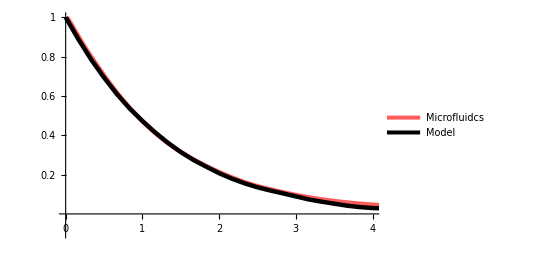

```mathematica
ListLinePlot[{Transpose@{Table[i/60,{i,1,Length[iptg1mmmcACF30minwindowsmooth]}],iptg1mmmcACF30minwindowsmooth},Map[{#[[1]],#[[2]]}&,metabsimMemory[[1]]]},PlotRange->{{0,4},{-.1,1}},PlotLegends->Placed[{"Microfluidcs","Model"},Right],PlotStyle->{{Thickness[0.008],RGBColor[1,0.36,0.36]},{Thickness[0.008],Black}},AxesStyle->Directive[Black, 20],Ticks->{Automatic,{0.2,0.4,0.6,0.8,1}},AspectRatio->.65]
```

```mathematica
{iptg1000um630growthACFsmooth,iptg1000um630mcACFsmooth,iptg1000um630betaxACFsmooth}=Import["C:\\Users\\Zhang Lab\\Desktop\\New folder\\1000um630ACFsmooth.txt","Table"];
```

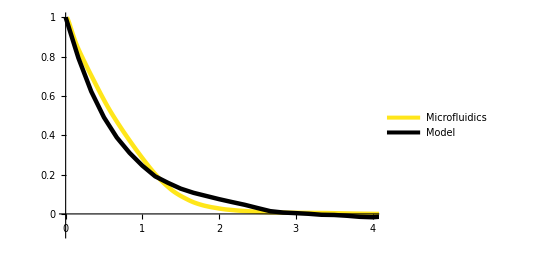

```mathematica
ListLinePlot[{Transpose@{Table[i/60,{i,1,Length[iptg1000um630betaxACFsmooth]}],iptg1000um630betaxACFsmooth},Map[{#[[1]],#[[2]]}&,metabsimMemory[[3]]]},PlotRange->{{0,4},{-.1,1}},
PlotLegends->Placed[{"Microfluidics","Model"},Right],
PlotStyle->{{Thickness[0.008],RGBColor[1,0.9,0.1]},{Thickness[0.008],Black}},AxesStyle->Directive[Black, 20],Ticks->{Automatic,{0,0.2,0.4,0.6,0.8,1}},AspectRatio->.65]
```

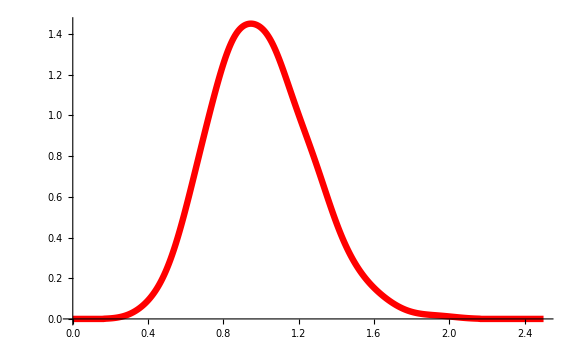

```mathematica
SmoothHistogram[keepMetabSS[[37,5]]/Mean[keepMetabSS[[37,5]]],.09,PlotStyle->{Thickness[0.008],Red},PlotRange->{{0,2.5},Automatic},ImageSize->Large]
```

```mathematica
exp630rawdata=Import["Z:\\Alex\\mfv2\\6-30-2020 tifs\\1000um iptg\\1000umclistaltalt.txt","Table"];//AbsoluteTiming
```

{1.688,Null}

```mathematica
MatrixForm[exp630rawdata[[1;;5]]]
```

({Cell,ID,Mother,ID,Time,(Frames),Age,(Frames),Relative,Age,Cell,age,Long,axis,(L),Short,axis,Area,Fluor1,sum,Fluor1,mean,Fluor2,sum,Fluor2,mean,Num,of,neighbors,dL,max,dL,min,Generation,Generation0,Growth,Rate}
{1044,40,2,1,0.0526316,18,18,7.02643,127,213108,1678.02,160647,1264.94,NaN,2,-1,1,1,0.0111484}
{1044,40,3,2,0.105263,18,18,6.98987,126,209972,1666.44,157056,1246.48,NaN,2,-1,1,1,0.0111484}
{1044,40,4,3,0.157895,18,18,7.25622,131,215520,1645.19,168914,1289.42,NaN,2,-1,1,1,0.0111484}
{1044,40,5,4,0.210526,18,18,7.30657,132,221393,1677.22,170253,1289.8,NaN,2,-1,1,1,0.0111484})

```mathematica
exp630rawdataselect=exp630rawdata[[All,{1,2,3,6,7,9,10,11,12,13}]];
```

```mathematica
MatrixForm[exp630rawdataselect[[1;;5]]]
```

(Cell | ID | Mother | (Frames) | Age | Relative | Age | Cell | age | Long
1044 | 40 | 2 | 18 | 18 | 127 | 213108 | 1678.02 | 160647 | 1264.94
1044 | 40 | 3 | 18 | 18 | 126 | 209972 | 1666.44 | 157056 | 1246.48
1044 | 40 | 4 | 18 | 18 | 131 | 215520 | 1645.19 | 168914 | 1289.42
1044 | 40 | 5 | 18 | 18 | 132 | 221393 | 1677.22 | 170253 | 1289.8)

```mathematica
exp630raw=exp630rawdataselect;
```

```mathematica
exp630raw[[2;;Length[exp630raw],{1,2,3,4,5,6}]]=Round[exp630raw[[2;;Length[exp630raw],{1,2,3,4,5,6}]]];
```

```mathematica
exp630raw[[2;;Length[exp630raw],{8}]]=N[exp630raw[[2;;Length[exp630raw],{8}]]-750];
```

```mathematica
exp630raw[[2;;Length[exp630raw],{10}]]=N[exp630raw[[2;;Length[exp630raw],{10}]]-963];
```

```mathematica
exp630raw[[2;;Length[exp630raw],{3}]]=N[exp630raw[[2;;Length[exp630raw],{3}]]*1/60];
```

```mathematica
MatrixForm[exp630raw[[1;;5]]]
```

(Cell | ID | Mother | (Frames) | Age | Relative | Age | Cell | age | Long
1044 | 40 | 0.0333333 | 18 | 18 | 127 | 213108 | 928.016 | 160647 | 301.937
1044 | 40 | 0.05 | 18 | 18 | 126 | 209972 | 916.444 | 157056 | 283.476
1044 | 40 | 0.0666667 | 18 | 18 | 131 | 215520 | 895.191 | 168914 | 326.42
1044 | 40 | 0.0833333 | 18 | 18 | 132 | 221393 | 927.22 | 170253 | 326.795)

```mathematica
exp630rawfljumpcut=removefljumps[exp630raw];//AbsoluteTiming
```

RFP Mean = -0.65333
RFP high = 194.137
RFP max = 1437.65
RFP low = -195.444
RFP min = -1404.55
YFP mean = -0.0847033
YFP high = 124.542
YFP max = 139.406
YFP low = -124.711
YFP min = -152.263

{8.94122,Null}

```mathematica
linsexp630=lineagefinder[exp630rawfljumpcut];//AbsoluteTiming
```

{11.7427,Null}

```mathematica
comblinexp630=combinelineages2fl[exp630raw,linsexp630];//AbsoluteTiming
```

{22.206,Null}

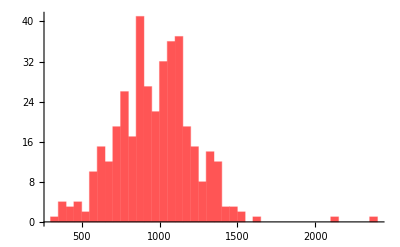

```mathematica
Histogram[Map[comblinexp630[[#]][[1,6]]&,Table[i,{i,Length[comblinexp630]}]],50,PlotRange->All,ChartStyle->Lighter[Red]]
```

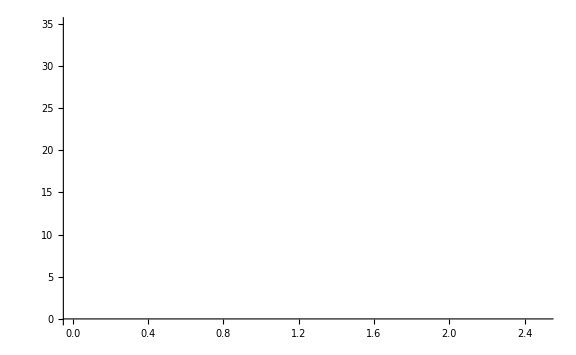
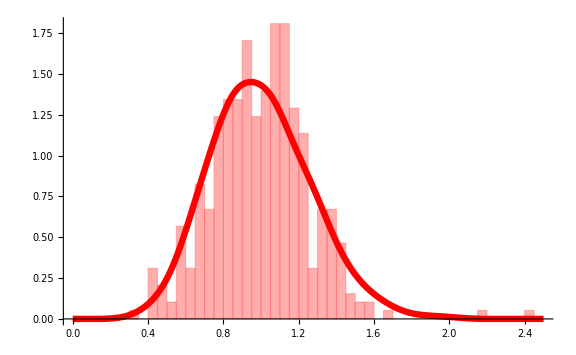

```mathematica
Overlay[{Histogram[{Map[comblinexp630[[#]][[1,6]]&,Table[i,{i,Length[comblinexp630]}]]/Mean[Map[comblinexp630[[#]][[1,6]]&,Table[i,{i,Length[comblinexp630]}]]]},30,PlotRange->{{0,2.5},Automatic},ChartStyle->{{EdgeForm[]},{RGBColor[1,0.36,0.36,0]}},Axes->{False,True},AxesStyle->{Directive[RGBColor[0,0,0,0],30],Directive[Black,30]},ImageSize->Large],Show[{Histogram[{Map[comblinexp630[[#]][[1,6]]&,Table[i,{i,Length[comblinexp630]}]]/Mean[Map[comblinexp630[[#]][[1,6]]&,Table[i,{i,Length[comblinexp630]}]]]},30,"PDF",PlotRange->{{0,2.5},Automatic},ChartStyle->RGBColor[1,0.36,0.36],Axes->{True,True},AxesStyle->{Directive[Black,30],Directive[RGBColor[0,0,0,0],30]},ImageSize->Large],SmoothHistogram[keepMetabSS[[37,5]]/Mean[keepMetabSS[[37,5]]],.09,PlotStyle->{Thickness[0.008],Red},PlotRange->{{0,2.5},Automatic},ImageSize->Large]}]}]
```

```mathematica
DOD=Map[comblinexp630[[#]][[1,6]]&,Table[i,{i,Length[comblinexp630]}]];
```

```mathematica
StandardDeviation[DOD]
```

252.459

```mathematica
Mean[DOD]
```

972.179

```mathematica
noiseofDOD=(StandardDeviation[DOD]/Mean[DOD])^2
```

0.0674356

```mathematica
noiseofDODsim=(StandardDeviation[keepMetabSS[[37,5]]]/Mean[keepMetabSS[[37,5]]])^2
```

0.0673842

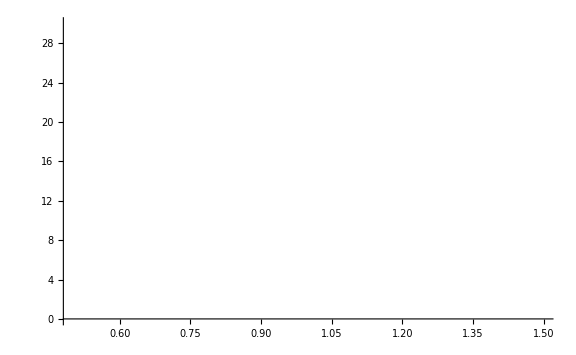
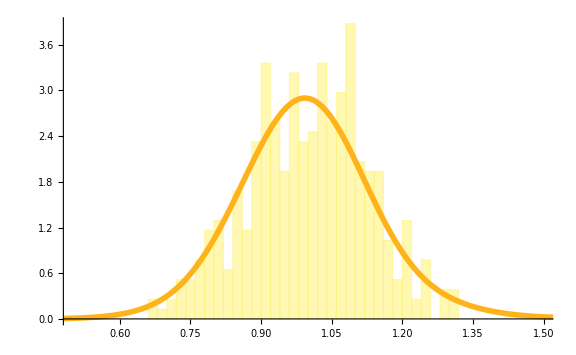

```mathematica
Overlay[{Histogram[{Map[comblinexp630[[#]][[1,7]]&,Table[i,{i,Length[comblinexp630]}]]/Mean[Map[comblinexp630[[#]][[1,7]]&,Table[i,{i,Length[comblinexp630]}]]]},30,PlotRange->{{0.5,1.5},Automatic},ChartStyle->{{EdgeForm[]},{RGBColor[1,0.95,0.4,0]}},Axes->{False,True},AxesStyle->{Directive[RGBColor[0,0,0,0],30],Directive[Black,30]},ImageSize->Large],Show[{Histogram[{Map[comblinexp630[[#]][[1,7]]&,Table[i,{i,Length[comblinexp630]}]]/Mean[Map[comblinexp630[[#]][[1,7]]&,Table[i,{i,Length[comblinexp630]}]]]},30,"PDF",PlotRange->{{0.5,1.5},Automatic},ChartStyle->RGBColor[1,0.95,0.4],Axes->{True,True},AxesStyle->{Directive[Black,30],Directive[RGBColor[0,0,0,0],30]},ImageSize->Large],SmoothHistogram[keepMetabSS[[37,7]]/Mean[keepMetabSS[[37,7]]],.09,PlotStyle->{Thickness[0.007],RGBColor[1,0.7,0.1]},PlotRange->{{0,2.5},Automatic},ImageSize->Large]}]}]
```

```mathematica
Betax=Map[comblinexp630[[#]][[1,7]]&,Table[i,{i,Length[comblinexp630]}]];
```

```mathematica
StandardDeviation[Betax]
```

44.4632

```mathematica
Mean[Betax]
```

346.29

```mathematica
noiseofbetax=(StandardDeviation[Betax]/Mean[Betax])^2
```

0.0164863

```mathematica
noiseofbetaxsim=(StandardDeviation[keepMetabSS[[37,7]]]/Mean[keepMetabSS[[37,7]]])^2
```

0.0152859

```mathematica
daughter227=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\iptg1mmrawtxt.txt","Table"]
```

{{CellID,MotherID,Time(Frames),Cellage,Longaxis(L),Area,Fluor1sum,Fluor1mean,Fluor2sum,Fluor2mean},{1,0,0.0166667,87,13,77,260132,2531.34,113581,279.078},164509,{16416,13255,6.66667,4,12,72,324926,3665.86,112243,362.931},{16416,13255,6.68333,4,12,78,358606,3750.51,123412,386.205}}
 |  |  |  |

```mathematica
Length[daughter227]
```

164513

```mathematica
daughter227[[2;;Length[daughter227],{7}]]=N[(daughter227[[2;;Length[daughter227],{8}]])*daughter227[[2;;Length[daughter227],{6}]]];
```

```mathematica
daughter227[[2;;Length[daughter227],{9}]]=N[(daughter227[[2;;Length[daughter227],{10}]])*daughter227[[2;;Length[daughter227],{6}]]];
```

```mathematica
daughter227[[2;;Length[daughter227],{8}]]=N[(daughter227[[2;;Length[daughter227],{8}]])*daughter227[[2;;Length[daughter227],{6}]]/10258];
```

```mathematica
daughter227[[2;;Length[daughter227],{10}]]=N[(daughter227[[2;;Length[daughter227],{8}]])*daughter227[[2;;Length[daughter227],{6}]]/10258];
```

```mathematica
MatrixForm[daughter227[[1;;5]]]
```

(CellID | MotherID | Time(Frames) | Cellage | Longaxis(L) | Area | Fluor1sum | Fluor1mean | Fluor2sum | Fluor2mean
1 | 0 | 0.0166667 | 87 | 13 | 77 | 194913. | 19.0011 | 21489. | 0.142628
1 | 0 | 0.0333333 | 87 | 14 | 83 | 209188. | 20.3927 | 21896. | 0.165002
1 | 0 | 0.05 | 87 | 14 | 80 | 202412. | 19.7321 | 17591. | 0.153887
1 | 0 | 0.0666667 | 87 | 13 | 83 | 204246. | 19.9109 | 21626. | 0.161104)

```mathematica
daughter227data=momdaughtconnect[daughter227];//AbsoluteTiming
```

{104.332,Null}

```mathematica
Length[daughter227data]
```

450

```mathematica
MatrixForm[daughter227data[[1;;5]]]
```

(parent | d1 | d2 | motherfl | d1fl | d2fl | motherfl2 | d1fl2 | d2fl2 | dmean | rootntot/2
20 | 848 | 849 | 452467. | 106267. | 288375. | 44577. | 14327. | 30050. | 197321. | 336.328
654 | 879 | 880 | 711370. | 337971. | 323237. | 57960. | 26025. | 27761. | 330604. | 421.714
159 | 885 | 886 | 712460. | 334873. | 319501. | 58832. | 29877. | 28320. | 327187. | 422.037
49 | 923 | 924 | 881592. | 434023. | 452660. | 47721. | 27055. | 22868. | 443342. | 469.466)

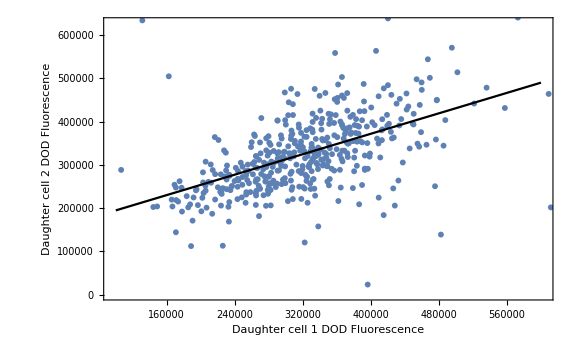

```mathematica
Show[ListPlot[
Transpose@{daughter227data[[All,5]],daughter227data[[All,6]]},
ImageSize-> Large,Frame->True,LabelStyle->Directive[Black,Medium],
FrameLabel->{"Daughter cell 1 DOD Fluorescence","Daughter cell 2 DOD Fluorescence"}],Plot[lm[x],{x,100000,600000},PlotStyle->Black]]
```

```mathematica
data=Map[{daughter227data⟦#,5⟧,daughter227data⟦#,6⟧}&,Range[2,450]];
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[135561.+0.591037 x]

```mathematica
N[Correlation[data[[All,1]],data[[All,2]]]]
```

0.532032

```mathematica
PairedTTest[{data[[All,1]],data[[All,2]]}]
```

0.332053

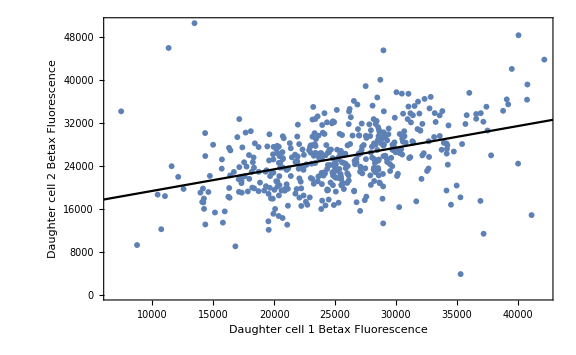

```mathematica
Show[ListPlot[
Transpose@{daughter227data[[All,8]],daughter227data[[All,9]]},
ImageSize-> Large,Frame->True,LabelStyle->Directive[Black,Medium],
FrameLabel->{"Daughter cell 1 Betax Fluorescence","Daughter cell 2 Betax Fluorescence"}],Plot[lmb[x],{x,0,45000},PlotStyle->Black]]
```

```mathematica
datab=Map[{daughter227data⟦#,8⟧,daughter227data⟦#,9⟧}&,Range[2,450]];
```

```mathematica
lmb=LinearModelFit[datab,x,x]
```

FittedModel[15271.2+0.402095 x]

```mathematica
N[Correlation[datab[[All,1]],datab[[All,2]]]]
```

0.398026

```mathematica
PairedTTest[{datab[[All,1]],datab[[All,2]]}]
```

0.54269

```mathematica
test630=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\1000umclistaltalt.txt","Table"];
```

```mathematica
MatrixForm[test630[[1;;5]]]
```

({Cell,ID,Mother,ID,Time,(Frames),Age,(Frames),Relative,Age,Cell,age,Long,axis,(L),Short,axis,Area,Fluor1,sum,Fluor1,mean,Fluor2,sum,Fluor2,mean,Num,of,neighbors,dL,max,dL,min,Generation,Generation0,Growth,Rate}
{1044,40,2,1,0.0526316,18,18,7.02643,127,213108,1678.02,160647,1264.94,NaN,2,-1,1,1,0.0111484}
{1044,40,3,2,0.105263,18,18,6.98987,126,209972,1666.44,157056,1246.48,NaN,2,-1,1,1,0.0111484}
{1044,40,4,3,0.157895,18,18,7.25622,131,215520,1645.19,168914,1289.42,NaN,2,-1,1,1,0.0111484}
{1044,40,5,4,0.210526,18,18,7.30657,132,221393,1677.22,170253,1289.8,NaN,2,-1,1,1,0.0111484})

```mathematica
test6300=test630[[All,{1,2,3,6,7,9,10,11,12,13}]];
```

```mathematica
test6300[[2;;Length[test6300],{1,2,3,4,5,6}]]=Round[test6300[[2;;Length[test6300],{1,2,3,4,5,6}]]];
```

```mathematica
test6300[[2;;Length[test6300],{8}]]=N[test6300[[2;;Length[test6300],{8}]]-750];
```

```mathematica
test6300[[2;;Length[test6300],{10}]]=N[test6300[[2;;Length[test6300],{10}]]-963];
```

```mathematica
test6300[[2;;Length[test6300],{3}]]=N[test6300[[2;;Length[test6300],{3}]]*1/60];
```

```mathematica
test6300cut=removefljumps[test6300];
```

RFP Mean = -0.65333
RFP high = 194.137
RFP max = 1437.65
RFP low = -195.444
RFP min = -1404.55
YFP mean = -0.0847033
YFP high = 124.542
YFP max = 139.406
YFP low = -124.711
YFP min = -152.263

```mathematica
linstest6300cut=lineagefinder[test6300cut];//AbsoluteTiming
```

{18.4527,Null}

```mathematica
comblintest630=combinelineages2fl[test6300,linstest6300cut];//AbsoluteTiming
```

{36.4748,Null}

```mathematica
comblinmultiplytest630=combinelineagesmulitply2fl[test6300,linstest6300cut];//AbsoluteTiming
```

{34.19,Null}

```mathematica
growthtest630noextrap=growthratecalcsupnoextrap[comblinmultiplytest630,30,comblintest630];//AbsoluteTiming
```

387

{5.76435,Null}

```mathematica
growthtest630cellphasenoextrap=addcellphase[growthtest630noextrap];//AbsoluteTiming
```

{0.130164,Null}

```mathematica
avgcellphasetest630nofit=averagecellphasenofitting[growthtest630cellphasenoextrap,20];
```

```mathematica
avgcellphasetest630noextrap=averagecellphase[growthtest630cellphasenoextrap,growthtest630noextrap];//AbsoluteTiming
```

{55.9063,Null}

```mathematica
normcellphasetest630noextrap=normcellphase[avgcellphasetest630noextrap,growthtest630cellphasenoextrap];//AbsoluteTiming
```

{1.02989,Null}

```mathematica
combnormcellphasetest630noextrap=combnormcellphase[normcellphasetest630noextrap,growthtest630noextrap];//AbsoluteTiming
```

{0.47741,Null}

```mathematica
{avggrowthplottest630noextrap,avgmcplottest630noextrap,avgbetaxplottest630noextrap}={avgflforplot[Map[Transpose@{#[[All,1]],#[[All,10]]}&,combnormcellphasetest630noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,11]]}&,combnormcellphasetest630noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,12]]}&,combnormcellphasetest630noextrap]]};//AbsoluteTiming
```

{35.9726,Null}

```mathematica
{test630growthwithrepeatnoextrap,test630growthwithrepeatnosubnoextrap,test630mcwithrepeatnoextrap,test630mcwithrepeatnosubnoextrap,test630betaxwithrepeatnoextrap,test630betaxwithrepeatnosubnoextrap}={convertforcross[growthminuspopmean[combnormcellphasetest630noextrap,10,avggrowthplottest630noextrap],10,5],convertforcross[growthminuspopmean[combnormcellphasetest630noextrap,10,0],10,5],convertforcross[growthminuspopmean[combnormcellphasetest630noextrap,11,avgmcplottest630noextrap],11,5],convertforcross[growthminuspopmean[combnormcellphasetest630noextrap,11,0],11,5],convertforcross[growthminuspopmean[combnormcellphasetest630noextrap,12,avgbetaxplottest630noextrap],12,5], convertforcross[growthminuspopmean[combnormcellphasetest630noextrap,12,0],12,5]};//AbsoluteTiming
```

{80.0348,Null}

```mathematica
SetSharedVariable[exp227growthwithrepeatnoextrap,exp227growthwithrepeatnosubnoextrap,exp227mcwithrepeatnoextrap,exp227mcwithrepeatnosubnoextrap,exp227betaxwithrepeatnoextrap,exp227betaxwithrepeatnosubnoextrap];
```

```mathematica
DistributeDefinitions[austinUBcompositecrosscorrvars,austinBIASEDcompositecrosscorrvars,individualaustinUBcompositecrosscorrvars,individualaustinBIASEDcompositecrosscorrvars];
```

```mathematica
{test630growthABiasedACFnoextrap,test630mcABiasedACFnoextrap,test630betaxABiasedACFnoextrap,test630mcgrowthABACFnoextrap,test630betaxgrowthABACFnoextrap,test630mcbetaxABACFnoextrap}=Parallelize[{austinBIASEDcompositecrosscorrvars[test630growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvars[test630mcwithrepeatnoextrap],austinBIASEDcompositecrosscorrvars[test630betaxwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[test630mcwithrepeatnoextrap,test630growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[test630betaxwithrepeatnoextrap,test630growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[test630mcwithrepeatnoextrap,test630betaxwithrepeatnoextrap]}];//AbsoluteTiming
```

{4591.17,Null}

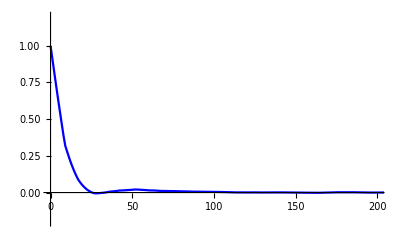

```mathematica
ListLinePlot[{Transpose@{Table[i,{i,0,Length[test630growthABiasedACFnoextrap]-1,1}],test630growthABiasedACFnoextrap}},PlotRange->{{0,200},{-.2,1.2}},PlotStyle->{Blue}]
```

```mathematica
growthtest630noextrapessential=growthtest630noextrap[[1;;,1;;,{1,2,4,6,7}]];
```

```mathematica
testset=RandomChoice[Table[i,{i,1,320}],50]
```

{252,65,293,172,148,114,31,74,216,287,225,34,120,164,156,160,261,29,150,202,160,203,148,277,137,14,40,191,174,224,43,210,46,214,104,93,187,268,149,286,171,184,4,93,120,112,23,223,208,119}

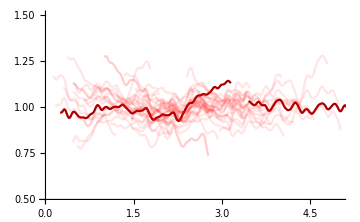

```mathematica
Show[{ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,1]&,{313,123}],PlotRange->{{0,5},{0.5,1.5}},PlotStyle->Darker[Red],ImageSize->Medium,AxesStyle->Directive[Black,20]],ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,1]&,testset],PlotRange->All,PlotStyle->Directive[Opacity[0.1],Red]]}]
```

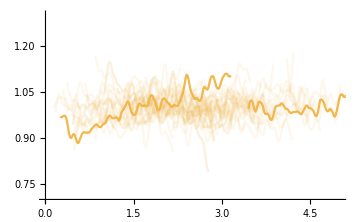

```mathematica
Show[{ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,3]&,{313,123}],PlotRange->{{0,5},{0.7,1.3}},PlotStyle->RGBColor["#f2b74d"],ImageSize->Medium,AxesStyle->Directive[Black,20]],ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,3]&,testset],PlotRange->All,PlotStyle->Directive[Opacity[0.1],RGBColor["#f2b74d"]]]}]
```

```mathematica
proteincurvesim=metabgensteadystate1[0,2.1,0,0,0,14,0.02,2000,0.2,1];//AbsoluteTiming
```

{3117.77,Null}

```mathematica
proteincurvesim2=metabmaintainsteadystate1[proteincurvesim[[1]],0,2.1,0,0,0,14,0.02,2000,0.2,1];//AbsoluteTiming
```

{0.0900114,Null}

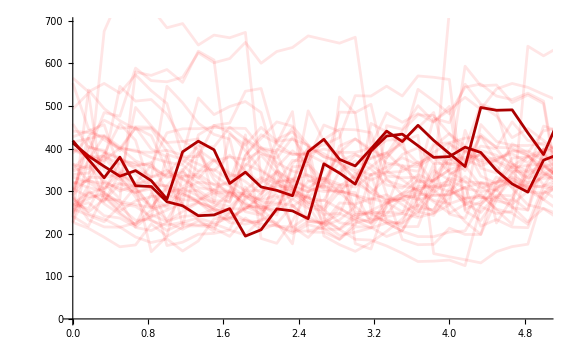

```mathematica
Show[{ListLinePlot[{Transpose@{proteincurvesim2[[All,1]],proteincurvesim2[[All,5,45]]},Transpose@{proteincurvesim2[[All,1]],proteincurvesim2[[All,5,48]]}},PlotRange->{{0,5},Automatic},PlotStyle->Darker[Red],ImageSize->Large,AxesStyle->Directive[Black,20]],ListLinePlot[Map[Transpose@{proteincurvesim2[[All,1]],proteincurvesim2[[All,5,#]]}&,Range[40]],ImageSize->Large,PlotRange->{{0,5},Automatic},PlotStyle->Directive[Opacity[0.1],Red]]}]
```

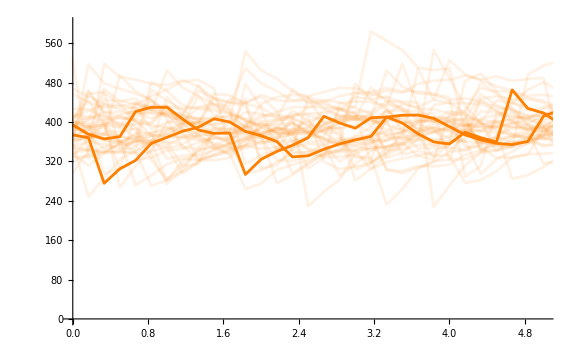

```mathematica
Show[{ListLinePlot[{Transpose@{proteincurvesim2[[All,1]],proteincurvesim2[[All,7,46]]},Transpose@{proteincurvesim2[[All,1]],proteincurvesim2[[All,7,48]]}},PlotRange->{{0,5},{0,600}},PlotStyle->Orange,ImageSize->Large,AxesStyle->Directive[Black,20]],ListLinePlot[Map[Transpose@{proteincurvesim2[[All,1]],proteincurvesim2[[All,7,#]]}&,Range[40]],ImageSize->Large,PlotRange->{{0,5},{0,600}},PlotStyle->Directive[Opacity[0.1],Orange]]}]
```

```mathematica
exp227rawdata=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\iptg1mmrawtxt.txt","Table"];//AbsoluteTiming
```

{3.65076,Null}

```mathematica
testexp227cut=removefljumps[exp227rawdata];
```

RFP Mean = -0.438949
RFP high = 812.338
RFP max = 18401.5
RFP low = -813.215
RFP min = -23766.4
YFP mean = -0.0150807
YFP high = 153.572
YFP max = 1288.14
YFP low = -153.602
YFP min = -1250.99

```mathematica
linstestexp227cut=lineagefinder[testexp227cut];//AbsoluteTiming
```

{46.3093,Null}

```mathematica
comblintestexp227=combinelineages2fl[exp227rawdata,linstestexp227cut];//AbsoluteTiming
```

{131.42,Null}

```mathematica
comblinmultiplytest630=combinelineagesmulitply2fl[exp227rawdata,linstestexp227cut];//AbsoluteTiming
```

{121.63,Null}

```mathematica
comblinmultiplytestexp227=comblinmultiplytest630;
```

```mathematica
growthtestexp227noextrap=growthratecalcsupnoextrap[comblinmultiplytestexp227,30,comblintestexp227];//AbsoluteTiming
```

799

{20.3353,Null}

```mathematica
growthexp227cellphasenoextrap=addcellphase[growthtestexp227noextrap];//AbsoluteTiming
```

{0.323117,Null}

```mathematica
avgcellphaseexp227nofit=averagecellphasenofitting[growthexp227cellphasenoextrap,20];
```

```mathematica
avgcellphaseexp227noextrap=averagecellphase[growthexp227cellphasenoextrap,growthtestexp227noextrap];//AbsoluteTiming
```

{897.179,Null}

```mathematica
normcellphaseexp227noextrap=normcellphase[avgcellphaseexp227noextrap,growthexp227cellphasenoextrap];//AbsoluteTiming
```

{2.61193,Null}

```mathematica
combnormcellphaseexp227noextrap=combnormcellphase[normcellphaseexp227noextrap,growthtestexp227noextrap];//AbsoluteTiming
```

{1.25753,Null}

```mathematica
{avggrowthplotexp227noextrap,avgmcplotexp227noextrap,avgbetaxplotexp227noextrap}={avgflforplot[Map[Transpose@{#[[All,1]],#[[All,10]]}&,combnormcellphaseexp227noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,11]]}&,combnormcellphaseexp227noextrap]],avgflforplot[Map[Transpose@{#[[All,1]],#[[All,12]]}&,combnormcellphaseexp227noextrap]]};//AbsoluteTiming
```

{154.32,Null}

```mathematica
{exp227growthwithrepeatnoextrap,exp227growthwithrepeatnosubnoextrap,exp227mcwithrepeatnoextrap,exp227mcwithrepeatnosubnoextrap,exp227betaxwithrepeatnoextrap,exp227betaxwithrepeatnosubnoextrap}={convertforcross[growthminuspopmean[combnormcellphaseexp227noextrap,10,avggrowthplotexp227noextrap],10,5],convertforcross[growthminuspopmean[combnormcellphaseexp227noextrap,10,0],10,5],convertforcross[growthminuspopmean[combnormcellphaseexp227noextrap,11,avgmcplotexp227noextrap],11,5],convertforcross[growthminuspopmean[combnormcellphaseexp227noextrap,11,0],11,5],convertforcross[growthminuspopmean[combnormcellphaseexp227noextrap,12,avgbetaxplotexp227noextrap],12,5], convertforcross[growthminuspopmean[combnormcellphaseexp227noextrap,12,0],12,5]};//AbsoluteTiming
```

{238.54,Null}

```mathematica
SetSharedVariable[exp227growthwithrepeatnoextrap,exp227growthwithrepeatnosubnoextrap,exp227mcwithrepeatnoextrap,exp227mcwithrepeatnosubnoextrap,exp227betaxwithrepeatnoextrap,exp227betaxwithrepeatnosubnoextrap];
```

```mathematica
DistributeDefinitions[austinUBcompositecrosscorrvars,austinBIASEDcompositecrosscorrvars,individualaustinUBcompositecrosscorrvars,individualaustinBIASEDcompositecrosscorrvars];
```

```mathematica
{exp227growthABiasedACFnoextrap,exp227mcABiasedACFnoextrap,exp227betaxABiasedACFnoextrap,exp227mcgrowthABACFnoextrap,exp227betaxgrowthABACFnoextrap,exp227mcbetaxABACFnoextrap}=Parallelize[{austinBIASEDcompositecrosscorrvars[exp227growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvars[exp227mcwithrepeatnoextrap],austinBIASEDcompositecrosscorrvars[exp227betaxwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[exp227mcwithrepeatnoextrap,exp227growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[exp227betaxwithrepeatnoextrap,exp227growthwithrepeatnoextrap],austinBIASEDcompositecrosscorrvarscross[exp227mcwithrepeatnoextrap,exp227betaxwithrepeatnoextrap]}];//AbsoluteTiming
```

{24045.4,Null}

```mathematica
Length[exp227growthABiasedACFnoextrap]
```

402

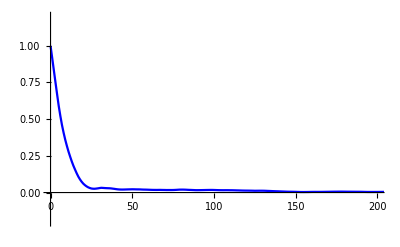

```mathematica
ListLinePlot[{Transpose@{Table[i,{i,0,401,1}],exp227growthABiasedACFnoextrap}},PlotRange->{{0,200},{-.2,1.2}},PlotStyle->{Blue}]
```

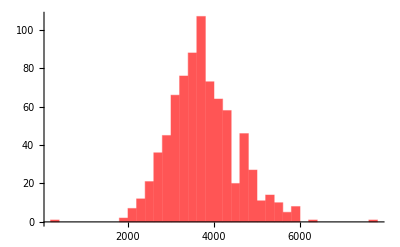

```mathematica
Histogram[Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]],50,PlotRange->All,ChartStyle->Lighter[Red]]
```

```mathematica
ol5000cell6h=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\ol5000cell6h.mx"];
```

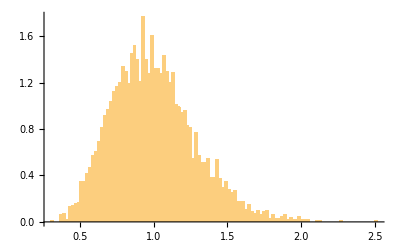

```mathematica
Histogram[ol5000cell6h[[1]][[1]]/ol5000cell6h[[1]][[6]]/Mean[ol5000cell6h[[1]][[1]]/ol5000cell6h[[1]][[6]]],100,"PDF"]
```

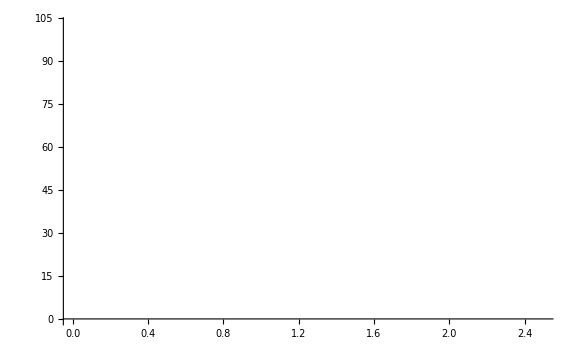
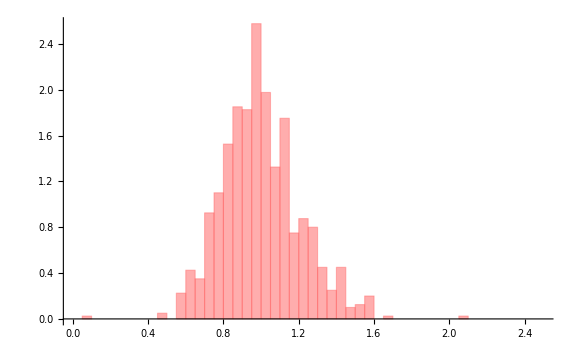

```mathematica
Overlay[{Histogram[{Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]]},30,PlotRange->{{0,2.5},Automatic},ChartStyle->{{EdgeForm[]},{RGBColor[1,0.36,0.36,0]}},Axes->{False,True},AxesStyle->{Directive[RGBColor[0,0,0,0],20],Directive[Black,20]},ImageSize->Large],Show[{Histogram[{Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]]},50,"PDF",PlotRange->{{0,2.5},Automatic},ChartStyle->RGBColor[1,0.36,0.36],Axes->{True,True},AxesStyle->{Directive[Black,20],Directive[RGBColor[0,0,0,0],20]},ImageSize->Large]}]}]
```

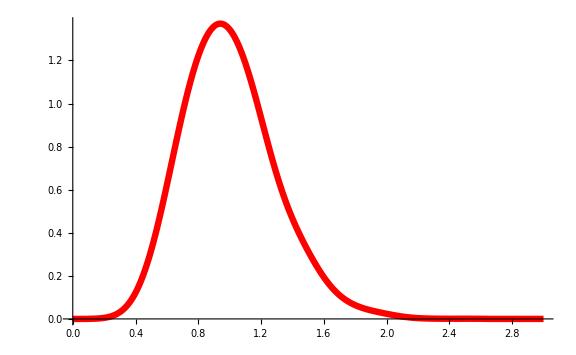

```mathematica
SmoothHistogram[ol5000cell6h[[1]][[1]]/ol5000cell6h[[1]][[6]]/Mean[ol5000cell6h[[1]][[1]]/ol5000cell6h[[1]][[6]]],0.1,PlotStyle->{Thickness[0.008],Red},PlotRange->{{0,3},Automatic},ImageSize->Large,Axes->{True,False}]
```

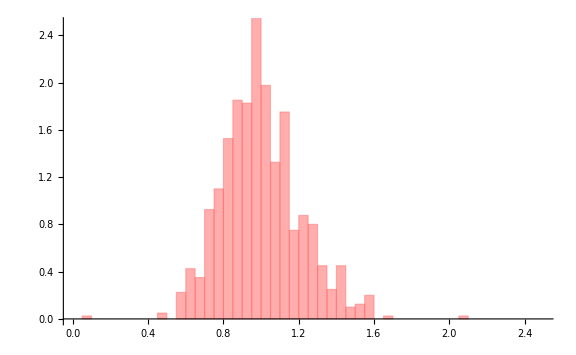

```mathematica
Histogram[{Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,6]]&,Table[i,{i,Length[comblintestexp227]}]]]},30,"PDF",PlotRange->{{0,2.5},{0,2.5}},ChartStyle->RGBColor[1,0.36,0.36],Axes->{True,True},AxesStyle->{Directive[Black,30],Directive[Black,30]},ImageSize->Large]
```

```mathematica
SmoothHistogram[ol5000cell6h[[1]][[1]]/ol5000cell6h[[1]][[6]]/Mean[ol5000cell6h[[1]][[1]]/ol5000cell6h[[1]][[6]]],0.1,PlotStyle->{Thickness[0.008],Red},PlotRange->{{0,3},Automatic},ImageSize->Large,Axes->{True,False}]
```

```mathematica
Histogram[{Map[comblinexp630[[#]][[1,7]]&,Table[i,{i,Length[comblinexp630]}]]/Mean[Map[comblinexp630[[#]][[1,7]]&,Table[i,{i,Length[comblinexp630]}]]]},30,PlotRange->{{0.5,1.5},Automatic},ChartStyle->{{EdgeForm[]},{RGBColor[1,0.95,0.4,0]}},Axes->{False,True},AxesStyle->{Directive[RGBColor[0,0,0,0],30],Directive[Black,30]},ImageSize->Large],
```

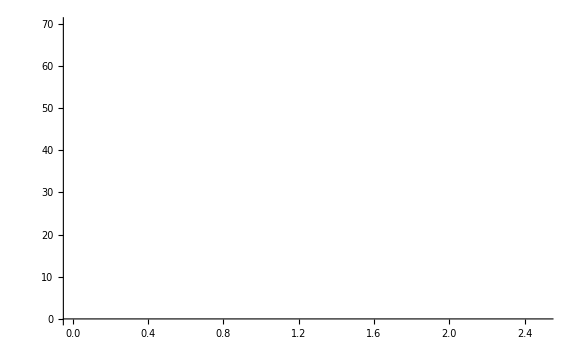
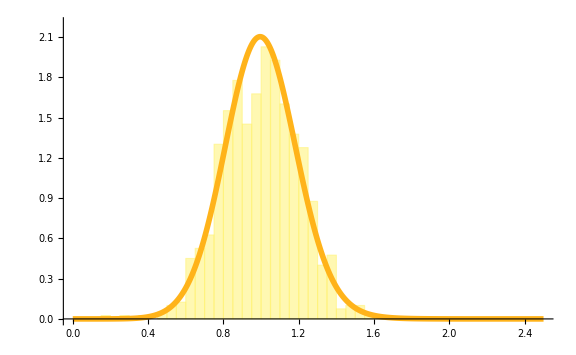

```mathematica
Overlay[{Histogram[{Map[comblintestexp227[[#]][[1,7]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,7]]&,Table[i,{i,Length[comblintestexp227]}]]]},30,PlotRange->{{0,2.5},{0,70}},ChartStyle->{{EdgeForm[]},{RGBColor[1,0.95,0.4,0]}},Axes->{False,True},AxesStyle->{Directive[RGBColor[0,0,0,0],20],Directive[Black,20]},ImageSize->Large],Show[{Histogram[{Map[comblintestexp227[[#]][[1,7]]&,Table[i,{i,Length[comblintestexp227]}]]/Mean[Map[comblintestexp227[[#]][[1,7]]&,Table[i,{i,Length[comblintestexp227]}]]]},30,"PDF",PlotRange->{{0,2.5},{0,2.2}},ChartStyle->RGBColor[1,0.95,0.4],Axes->{True,True},AxesStyle->{Directive[Black,20],Directive[RGBColor[0,0,0,0],20]},ImageSize->Large],SmoothHistogram[ol5000cell6h[[1]][[4]]/ol5000cell6h[[1]][[6]]/Mean[ol5000cell6h[[1]][[4]]/ol5000cell6h[[1]][[6]]],.15,PlotStyle->{Thickness[0.007],RGBColor[1,0.7,0.1]},PlotRange->{{0,2.5},Automatic},ImageSize->Large]}]}]
```